```mathematica
ClearAll["Global`*"]
w[p_,m_]=Sqrt[p*p+m*m];
absgradg[t_,u_,v_,p_]=√((-t*u*w[p,mb]/w[t*Q,ma]*Q^2+Q*p*v)^2+(w[t*Q,ma]*w[p,mb])^2+(t*Q*p)^2);
areafactor[t_,v_,p_]=√((v*(p*Q)/(w[p,mb]*w[t*Q,ma])*(1-(t^2*Q^2)/w[t*Q,ma]^2))^2+(1)^2+((t*Q*p)/(w[t*Q,ma]*w[p,mb]))^2);
ustar[t_,v_,p_]=(ma*Eabc+Q*p*t*v)/(w[t*Q,ma]*w[p,mb]);
```

```mathematica
s=Solve[1==ustar[t,v,p],v];
v1[t_,p_]=v/.s[[1]]//FullSimplify;
t1min[p_]=t/.Solve[0==D[v1[t,p],t],t][[2]]//FullSimplify;
vmin[p_]=v1[t1min[p],p]//FullSimplify;
s2=Solve[1==v1[t,p],t]//FullSimplify;
tmin[p_]=t/.s2[[1]]//FullSimplify;
tmax[p_]=t/.s2[[2]]//FullSimplify;
Print["v(t,p)|u==1:",v1[t,p], "(=:v1(t,p))"]
Print["v1=min(v1(t,p) at t=",t1min[p]]
Print["min(v1(t,p))=",vmin[p]]
Print["tmin(p)=",tmin[p]]
Print["tmax(p)=",tmax[p]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

v(t,p)|u==1:(-Eabc ma+√(mb^2+p^2) √(ma^2+Q^2 t^2))/(p Q t)(=:v1(t,p))

v1=min(v1(t,p) at t=(√(ma^2 (-Eabc^2+mb^2+p^2)))/(Eabc Q)

min(v1(t,p))=(Eabc (-Eabc ma+√(mb^2+p^2) √((ma^2 (mb^2+p^2))/Eabc^2)))/(p √(ma^2 (-Eabc^2+mb^2+p^2)))

tmin(p)=(Eabc ma p-√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

tmax(p)=(Eabc ma p+√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

```mathematica
Simplify[Series[1-vmin[p],p->Infinity],{Element[Eabc,Reals],Eabc>0}]
Simplify[Series[tmax[p]-tmin[p],p->Infinity],{Element[Eabc,Reals],Eabc>0}]
```

O[1/p]^1

(2 √((ma^2 (Eabc^2-mb^2) p^2)/Q^2))/mb^2+O[1/p]^2

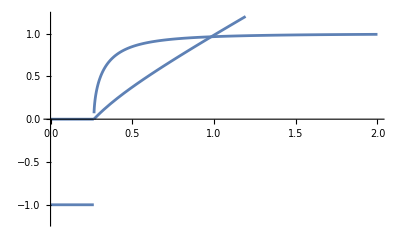

```mathematica
Q=1;
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];

LowerBoundV[p_]=If[Eabc^2<mb^2+p^2,vmin[p],-1];
BetterLowerBoundV[t_,p_]=Clip[v1[t,p],{-1,1}];
LowerBoundT[p_]=If[tmin[p]<0,0,tmin[p]];
Show[
Plot[LowerBoundV[p],{p,0,2},PlotRange->{Automatic,{-1.2,1.2}}],
Plot[LowerBoundT[p],{p,0,2},PlotRange->{Automatic,{-1.2,1.2}}]
]

Manipulate[
RegionPlot[LowerBoundT[p]<t&&BetterLowerBoundV[t,p]<v<1,{t,-0.1*tmax[p],1.1*tmax[p]},{v,LowerBoundV[p]-0.1*Abs[1-LowerBoundV[p]],1+0.1*Abs[1-LowerBoundV[p]]}],
{p,0.0001,2}
]
```

```mathematica
Install[StringJoin[NotebookDirectory[],"Cuhre-Linux"]];
Install[StringJoin[NotebookDirectory[],"Vegas-Linux"]];
```

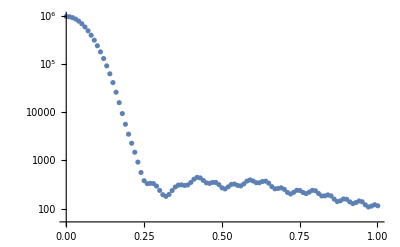

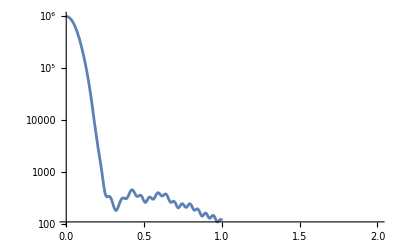

```mathematica
mydata=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/spec_20240806_151611/spectr1.txt"],"CSV"];
keys=mydata[[9]];
data=mydata[[10;;]];
ps=(Transpose@data)[[1]];
spec=(Transpose@data)[[2]];
logspecfunc=Interpolation[Transpose@{ps,Log[spec]}];
specfunc[x_]=If[x<Max[ps],Exp[logspecfunc[x]],0];

ListLogPlot[Transpose@{ps,spec}]
LogPlot[specfunc[x],{x,0,2*Max[ps]}]
```

```mathematica
Integrand[t_,v_,p_]=If[ustar[t,v,p]>1,t*specfunc[Q*t]*1/(√(ustar[t,v,p]^2-1))*1/(√(1-v^2))*areafactor[t,v,p]/absgradg[t,ustar[t,v,p],v,p],0]
```

If[(0.18+p t v)/(√(0.0196+p^2) √(0.36+t^2))>1,(t specfunc[Q t] areafactor[t,v,p])/(√(ustar[t,v,p]^2-1) √(1-v^2) absgradg[t,ustar[t,v,p],v,p]),0]

```mathematica
MyIntegral[p_]:=Cuhre[Integrand[t,v,p],{t,LowerBoundT[p],tmax[p]},{v,BetterLowerBoundV[t,p],1},Verbose->0][[1]][[1]]
ps=Array[#&,50,{0.001,1}]
```

{0.001,0.0213878,0.0417755,0.0621633,0.082551,0.102939,0.123327,0.143714,0.164102,0.18449,0.204878,0.225265,0.245653,0.266041,0.286429,0.306816,0.327204,0.347592,0.36798,0.388367,0.408755,0.429143,0.449531,0.469918,0.490306,0.510694,0.531082,0.551469,0.571857,0.592245,0.612633,0.63302,0.653408,0.673796,0.694184,0.714571,0.734959,0.755347,0.775735,0.796122,0.81651,0.836898,0.857286,0.877673,0.898061,0.918449,0.938837,0.959224,0.979612,1.}

```mathematica
decayspec=Map[MyIntegral,ps]
```

Cuhre::accuracy: Desired accuracy was not reached within 50115 function evaluations on 386 subregions.

General::stop: Further output of Cuhre::accuracy will be suppressed during this calculation.

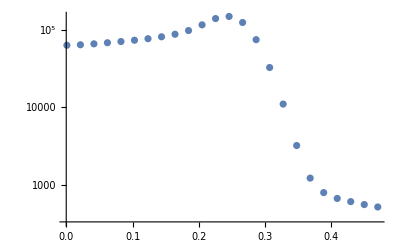

```mathematica
ListLogPlot[Transpose@{ps,decayspec}]
```